```mathematica
(*
Author: Oleg Kravchenko;
Date: 24/05/16;
*)
```

```mathematica
1D;
```

```mathematica
A={{0,κ},{1/ρ,0}}
{vals,vects}=Eigensystem[A]
P=Transpose@vects
dd=Inverse@P.A.P
Diagonal[dd,#]&/@{-1,1}//Simplify
```

{{0,κ},{1/ρ,0}}

{{-(√κ)/(√ρ),(√κ)/(√ρ)},{{-√κ √ρ,1},{√κ √ρ,1}}}

{{-√κ √ρ,√κ √ρ},{1,1}}

{{-(√κ)/(√ρ),0},{0,(√κ)/(√ρ)}}

{{0},{0}}

```mathematica
p0[x_]:=0
v0[x_]:=UnitBox[x-5]

(*f plus/minus waves*)
fp[ρ_,c_,x_]:=p0[x]+ρ c v0[x]
fm[ρ_,c_,x_]:=p0[x]-ρ c v0[x]
```

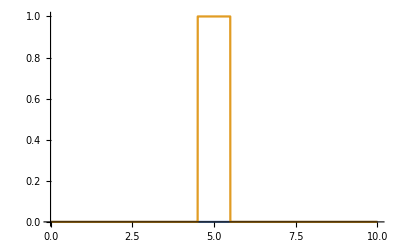
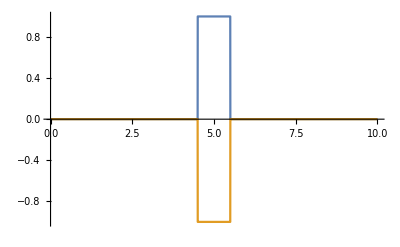

```mathematica
L=10;imgSz=350;
Row@{Plot[{p0[x],v0[x]},{x,0,L},PlotStyle->Thick],
Plot[{fp[1,1,x],fm[1,1,x]},{x,0,L},PlotStyle->Thick]}
```

```mathematica
Manipulate[
Column@{
Plot[{fp[c,ρ,x-c t],fm[c,ρ,x+c t]},{x,0,L},PlotStyle->Thick,ImageSize->imgSz],
Plot[{(fp[c,ρ,x-c t]+fm[c,ρ,x+c t])/2,(fp[c,ρ,x-c t]-fm[c,ρ,x+c t])/(2ρ c)},{x,0,L},PlotStyle->Thick,ImageSize->imgSz]
},
{c,0.1,1,0.1},
{ρ,1,5,1},
{t,0,100,1}
]
```

```mathematica
2D;
```

```mathematica
p02D[x_,y_]:=0
v02D[x_,y_]:=UnitBox[x-5]UnitBox[y-5]

(*f plus/minus waves*)
fp2D[ρ_,c_,x_,y_]:=p02D[x,y]+ρ c v02D[x,y]
fm2D[ρ_,c_,x_,y_]:=p02D[x,y]-ρ c v02D[x,y]
```

```mathematica
Lx=10;Ly=10;imgSz=350;
Row@{Plot3D[{p02D[x,y],v02D[x,y]},{x,0,Lx},{y,0,Ly},ImageSize->imgSz],
Plot3D[{fp2D[1,1,x,y],fm2D[1,1,x,y]},{x,0,Lx},{y,0,Ly},ImageSize->imgSz,Mesh->None,PlotPoints->50,PlotStyle->Opacity[0.5]]}
```

-Graphics3D--Graphics3D-

```mathematica
Manipulate[
Column@{
DensityPlot[{fp2D[c,ρ,x-c t,y-c t],fm[c,ρ,x+c t,y+c t]},{x,0,Lx},{y,0,Ly},Mesh->None,PlotPoints->50,ImageSize->imgSz],
DensityPlot[{(fp2D[c,ρ,x-c t,y-c t]+fm2D[c,ρ,x+c t,y+c t])/2,(fp2D[c,ρ,x-c t,y-c t]-fm2D[c,ρ,x+c t,y+c t])/(2ρ c)},{x,0,Lx},{y,0,Ly},Mesh->None,PlotPoints->50,ImageSize->imgSz]
},
{c,0.1,1,0.1},
{ρ,1,5,1},
{t,0,100,1}
]
```